# Mathematica Tutorial - 1

* Click Evaluation >> Evaluate Notebook

## Different Modes

Alt + 7 for text, Alt + 9 for math cell.
While inside any cell, Ctrl + 9 toggles on inline text/math and Ctrl + 0 toggles off that.
Clicking the Format >> Style from the top menu bar lets you select different format for the current cell.

To create a new cell below, type Ctrl + Shift + D.
Clicking anywhere, while the cursor is shown horizontal, you can enter to a new cell.

## Execute Commands

Restarting or clearing the variables.
Note the back qoute ( ` ), NOT a single qoute ( ‘ )!!

```mathematica
Clear["Global`*"]
```

```mathematica
3+7
```

10

Adding a semi colon supresses the output.

```mathematica
4+7;
```

## Basic Operations

Power is only ^ not **

```mathematica
(4/2)*3-7^8+7**8
```

-5764795+7**8

```mathematica
(4/2)*3-7^8+7^8
```

6

```mathematica
2485/3479
```

5/7

Ctrl + L lets you input the last command entered.

```mathematica
2485./3479
```

0.714286

To show upto 40 decimal places

```mathematica
SetPrecision[2485/3479,40]
```

0.7142857142857142857142857142857142857143

Numerical value of a float

```mathematica
N[2485/3479, 20]
```

0.71428571428571428571

```mathematica
1.0*10^(-6)
1.0*^-6
1*^-6
```

1.×10^-6

1.×10^-6

1/1000000

```mathematica
E
```

ⅇ

```mathematica
N[ⅇ]
```

2.71828

```mathematica
1.*E-6
```

-3.28172

```mathematica
Log[1.*^-6]
```

-13.8155

```mathematica
SetPrecision[%, 40]
```

-13.81551055796427363020484335720539093018

```mathematica
Exp[1.]
```

2.71828

```mathematica
Exp[1]
```

ⅇ

```mathematica
Log[Exp[1]]
```

1

```mathematica
Sqrt[10!]
```

720 √7

```mathematica
Pi
```

π

```mathematica
N[Pi]
```

3.14159

```mathematica
Log[x]
```

Log[x]

```mathematica
Log10[x]
```

Log[x]/Log[10]

```mathematica
Abs[x]
```

Abs[x]

```mathematica
Cos[x]
```

Cos[x]

```mathematica
Sin[Pi]
```

0

```mathematica
Sin[pi]
```

Sin[pi]

```mathematica
(2+3*I)/(5-4*I)
```

-2/41+(23 ⅈ)/41

Converting a complex no to polar form

```mathematica
Abs[%]* Exp[I * Arg[%]]
```

√(13/41) ⅇ^(ⅈ (π-ArcTan[23/2]))

```mathematica
N[√(13/41) ⅇ^(ⅈ (π-ArcTan[23/2]))]
```

-0.0487805+0.560976 ⅈ

Getting help and extended help. Clicking the >> opens the detailed help window.

```mathematica
?N
```

RowBox[{"N", "[", StyleBox["expr", "TI"], "]"}] gives the numerical value of StyleBox["expr", "TI"]. 
RowBox[{"N", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["n", "TI"]}], "]"}] attempts to give a result with StyleBox["n", "TI"]-digit precision.

```mathematica
??N
```

RowBox[{"N", "[", StyleBox["expr", "TI"], "]"}] gives the numerical value of StyleBox["expr", "TI"]. 
RowBox[{"N", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["n", "TI"]}], "]"}] attempts to give a result with StyleBox["n", "TI"]-digit precision.

Attributes[N]={Protected}
 
N/:Default[N,2]:={MachinePrecision,MachinePrecision}

Normal MachinePrecision is 16 digits. This can be checked.

```mathematica
N[MachinePrecision]
```

15.9546

## Sums and Products

```mathematica
Clear["Global`*"]
```

```mathematica
Sum[i^2,{i, 10}]
Sum[i^2, {i, 1, 10}]
Sum[i, {i, 0,10,2}]
Sum[i^2, {i, 1, n}]
Sum[i^2, i]
```

385

385

30

1/6 n (1+n) (1+2 n)

1/6 (-1+i) i (-1+2 i)

Summing the cos series

```mathematica
Sum[(-1)^i*x^(2*i)/(2*i)!,{i,0,2}]
```

1-x^2/2+x^4/24

```mathematica
Sum[(-1)^i*x^(2*i)/(2*i)!,{i,0,n}]
```

Cos[x]+((-1)^n x^(2+2 n) HypergeometricPFQ[{1},{3/2+n,2+n},-x^2/4])/((2 (1+n))!)

```mathematica
Sum[(-1)^i*x^(2*i)/(2*i)!,{i,0,Infinity}]
```

Cos[x]

```mathematica
Sum[(-1)^i*x^(2*i)/(2*i)!,i]
```

-1+Cos[x]-((-x^2)^i HypergeometricPFQ[{1},{1/2+i,1+i},-x^2/4])/Gamma[1+2 i]

The product works just like sum.

```mathematica
Product[(i^2+3*i-11)/(i+3),{i, 0, 10}]
```

-7781706512657/40435200

Use Esc prod Esc to enter ∏ and Ctrl+_ to enter the lower limit, then Ctrl+% for the upper limit. Use the Basic Math Assistant to enter symbolic inputs.

```mathematica
∏_(i=0)^10 (i^2+3i-11)/(i+3)
```

-7781706512657/40435200

Note: NSum[] and NProduct[] give numerical approximations to sum and product respectively.

```mathematica
Product[(i^2+3*i-11)/(i+3),{i, 0, n}]
```

-(2 Cos[(√53 π)/2] Gamma[5/2-(√53)/2+n] Gamma[5/2+(√53)/2+n])/(13 π Gamma[4+n])

```mathematica
N[%]
```

-(0.0208584 Gamma[-1.14005+n] Gamma[6.14005+n])/Gamma[4.+n]

## Symbolic Manipulations

```mathematica
Clear["Global'*"]
```

```mathematica
Sum[i,{i,1,n}]
```

1/2 n (1+n)

Use Esc sum Esc to enter ∑ and Ctrl+_ to enter the lower limit, then Ctrl+% for the upper limit.

```mathematica
∑_(i=1)^n i
```

1/2 n (1+n)

```mathematica
N[%]
```

0.5 n (1.+n)

```mathematica
Expand[%]
```

0.5 n+0.5 n^2

```mathematica
Factor[%]
```

0.5 n (1.+1. n)

Convert floating point no to fractions.

```mathematica
Rationalize[%]
```

1/2 n (1+n)

```mathematica
Factor[%]
```

1/2 n (1+n)

```mathematica
Expand[(x+y)^15]
```

x^15+15 x^14 y+105 x^13 y^2+455 x^12 y^3+1365 x^11 y^4+3003 x^10 y^5+5005 x^9 y^6+6435 x^8 y^7+6435 x^7 y^8+5005 x^6 y^9+3003 x^5 y^10+1365 x^4 y^11+455 x^3 y^12+105 x^2 y^13+15 x y^14+y^15

```mathematica
Simplify[Cos[x]^2+Sin[x]^2]
```

1

Trogonometric to Exponential conversion

```mathematica
TrigToExp[Sin[x]]
```

1/2 ⅈ ⅇ^(-ⅈ x)-1/2 ⅈ ⅇ^(ⅈ x)

```mathematica
Simplify[%]
```

-1/2 ⅈ ⅇ^(-ⅈ x) (-1+ⅇ^(2 ⅈ x))

```mathematica
ExpToTrig[%]
```

-1/2 ⅈ (Cos[x]-ⅈ Sin[x]) (-1+Cos[2 x]+ⅈ Sin[2 x])

```mathematica
Simplify[%]
```

Sin[x]

## Statements, Expressions, Functions & Procedures

```mathematica
Clear["Global'*"]
```

```mathematica
1+4
Exp[x]-1
```

5

-1+ⅇ^x

Normal assignment is done with = sign.
Delayed assignment is doen with := sign.

```mathematica
x=3
```

3

```mathematica
y=3*z^2+1
```

1+3 z^2

Explaining Delayed Assignment.
In the first case, y1 is calculated using the current value of x. So, once assigned, y1 is fixed.
In the second case, y2 is calculated each time using the then value of x. So value of y2 changes depending on x each time it is used.

```mathematica
y1=3*x^2+1
```

28

```mathematica
y2:=3*x^2+1
```

```mathematica
y2
```

28

```mathematica
x=4
```

4

```mathematica
y1
```

28

```mathematica
y2
```

49

Evaluation/Replacing/Substitution
/. is the ReplaceAll operator. The format is expr /. rule or expr /. {rule1, rule2, ..}

```mathematica
y/.z->2
```

13

```mathematica
?/.
```

RowBox[{StyleBox["expr", "TI"], "/.", StyleBox["rules", "TI"]}] applies a rule or list of rules in an attempt to transform each subpart of an expression StyleBox["expr", "TI"].

Functions

```mathematica
f[x_]:=x*Sin[x]
```

```mathematica
f[2]
```

2 Sin[2]

```mathematica
N[2 Sin[2]]
```

1.81859

```mathematica
R[x_,y_,z_]:=Sqrt[x*x+y*y+z*z]
```

```mathematica
R[1,2,3]
```

√14

Maple’s unapply( ) equivalent is Evaluate[ ]

```mathematica
g[z_]=Evaluate[3*z^2+1]
```

1+3 z^2

```mathematica
g[2]
```

13

```mathematica
?Evaluate
```

RowBox[{"Evaluate", "[", StyleBox["expr", "TI"], "]"}] causes StyleBox["expr", "TI"] to be evaluated even if it appears as the argument of a function whose attributes specify that it should be held unevaluated.

```mathematica
Clear[x]
```

```mathematica
p=x^2+sin(x)+1
```

1+sin x+x^2

```mathematica
f[x_]=Evaluate[p]
```

1+sin x+x^2

```mathematica
f[Pi/6]
```

1+π^2/36+(π sin)/6

```mathematica
Clear[x]
```

```mathematica
z=x*Sin[x]
```

x Sin[x]

```mathematica
zfun[x_]=Evaluate[z]
```

x Sin[x]

## Control Structures

```mathematica
?For
```

RowBox[{"For", "[", RowBox[{StyleBox["start", "TI"], ",", StyleBox["test", "TI"], ",", StyleBox["incr", "TI"], ",", StyleBox["body", "TI"]}], "]"}] executes StyleBox["start", "TI"], then repeatedly evaluates StyleBox["body", "TI"] and StyleBox["incr", "TI"] until StyleBox["test", "TI"] fails to give True.

```mathematica
For[i=1,i≤5,i++,
Print[i]
]
```

1

2

3

4

5

```mathematica
For[i=1, i≤5, i+=2,
Print[i]
]
```

1

3

5

```mathematica
?While
```

RowBox[{"While", "[", RowBox[{StyleBox["test", "TI"], ",", StyleBox["body", "TI"]}], "]"}] evaluates StyleBox["test", "TI"], then StyleBox["body", "TI"], repetitively, until StyleBox["test", "TI"] first fails to give True.

```mathematica
x=1
```

1

```mathematica
While[x<5,
Print[x];
x++;
]
```

1

2

3

4

```mathematica
x=7
```

7

```mathematica
?If
```

RowBox[{"If", "[", RowBox[{StyleBox["condition", "TI"], ",", StyleBox["t", "TI"], ",", StyleBox["f", "TI"]}], "]"}] gives StyleBox["t", "TI"] if StyleBox["condition", "TI"] evaluates to True, and StyleBox["f", "TI"] if it evaluates to False. 
RowBox[{"If", "[", RowBox[{StyleBox["condition", "TI"], ",", StyleBox["t", "TI"], ",", StyleBox["f", "TI"], ",", StyleBox["u", "TI"]}], "]"}] gives StyleBox["u", "TI"] if StyleBox["condition", "TI"] evaluates to neither True nor False.

```mathematica
If[x<10,
Print["x<10"],
Print["x>10"]
]
```

x<10

## Solving Equations

single Equation (subscripted variable)

```mathematica
Clear["Global`*"]
```

```mathematica
Solve[a x^2+b x + c, x]
```

Solve::naqs: c + b\ x + a\ x^2 is not a quantified system of equations and inequalities.

Solve[c+b x+a x^2,x]

Note: The expression to be solved must be an equation, e.g. == 0 needs to be specified.

```mathematica
Solve[a x^2+b x + c==0, x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

```mathematica
x/.{{x->(-b-√(b^2-4 a c))/(2 a)},{x->(-b+√(b^2-4 a c))/(2 a)}}
```

{(-b-√(b^2-4 a c))/(2 a),(-b+√(b^2-4 a c))/(2 a)}

```mathematica
y=a*x^2+b*x+c==0
```

c+b x+a x^2==0

```mathematica
Solve[y,{x}]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

```mathematica
y/.x->a/2
```

a^3/4+(a b)/2+c==0

```mathematica
Roots[x^2-1==0, x]
```

x==1||x==-1

```mathematica
Roots[x^2+1==0, x]
```

x==ⅈ||x==-ⅈ

```mathematica
ans=Solve[y,x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

```mathematica
ans[[1]]
```

{x→(-b-√(b^2-4 a c))/(2 a)}

```mathematica
x/.ans[[2]]
```

(-b+√(b^2-4 a c))/(2 a)

```mathematica
NSolve[x*Sin[x]-1,x]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[-1+x Sin[x],x]

```mathematica
NSolve[x*Sin[x]-1==0 && 0<x<6,x]
```

{{x→1.11416},{x→2.7726}}

Simultaneous Equations

```mathematica
eqn1=a+3*b+4*c==41;
eqn2=5*a+6*b+7*c==20;
```

```mathematica
Solve[eqn1 && eqn2, {a, b}]
```

{{a→1/3 (-62+c),b→1/9 (185-13 c)}}

## Plotting Along

```mathematica
Clear["Global`*"]
```

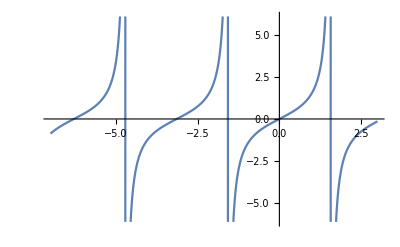

```mathematica
Plot[Tan[x], {x, -7, 3}]
```

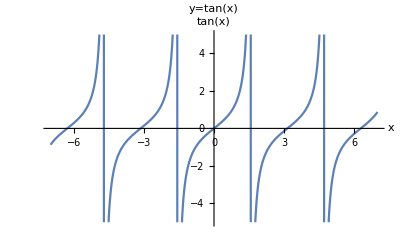

```mathematica
Plot[Tan[x], {x, -7, 7},
PlotRange->{-5,5},
AxesLabel->{"x", "tan(x)"},
PlotLabel->"y=tan(x)"
]
```

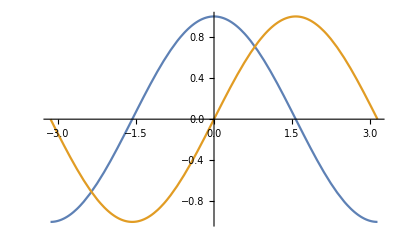

```mathematica
Plot[{Cos[x], Sin[x]}, {x, -Pi, Pi}]
```

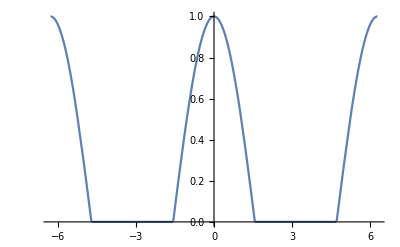

```mathematica
Plot[Max[0, Cos[x]], {x,-2*Pi, 2*Pi}]
```

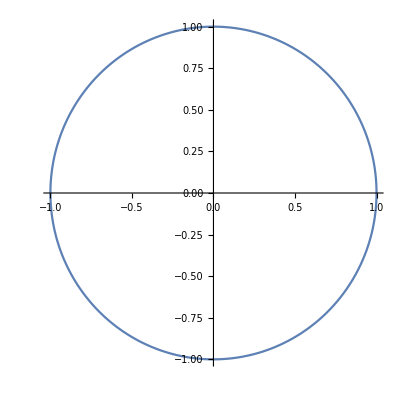

```mathematica
ParametricPlot[{Sin[x], Cos[x]}, {x, 0, 2*Pi}]
```

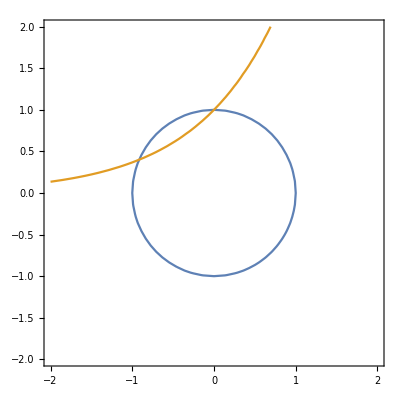

```mathematica
ContourPlot[{x^2+y^2==1,y==Exp[x]}, {x, -2, 2}, {y, -2, 2},
Axes->True
]
```

```mathematica
Plot3D[x*(x^2-3*y^2), {x, -1, 1}, {y, -1,1},
PlotLabel->"Saddle"
]
```

-Graphics3D-

## Plotting of Data

```mathematica
Xdata = {1, 2, 3, 6, 10}
```

{1,2,3,6,10}

```mathematica
Ydata={1, 4, 9, 36, 100}
```

{1,4,9,36,100}

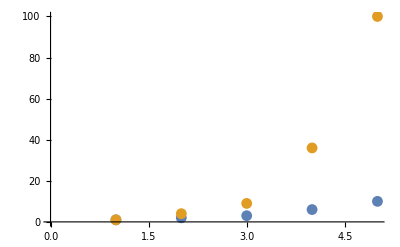

```mathematica
ListPlot[{Xdata, Ydata}]
```

## Calculus

Differentiation

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_]:=Log[x]/(1-x)
```

```mathematica
D[f[x],x]
```

1/((1-x) x)+Log[x]/(1-x)^2

```mathematica
D[f[x],{x,2}]
```

-1/((1-x) x^2)+2/((1-x)^2 x)+(2 Log[x])/(1-x)^3

```mathematica
f'[x]
```

1/((1-x) x)+Log[x]/(1-x)^2

```mathematica
f''[x]
```

-1/((1-x) x^2)+2/((1-x)^2 x)+(2 Log[x])/(1-x)^3

```mathematica
D[Sin[x]^y,x]
```

y Cos[x] Sin[x]^(-1+y)

```mathematica
D[Sin[x]^y,x, y]
```

Cos[x] Sin[x]^(-1+y)+y Cos[x] Log[Sin[x]] Sin[x]^(-1+y)

```mathematica
D[f[x,y,x],x,x,y,z,z,z]
```

0

```mathematica
g[x_]=D[f[x],x]
```

1/((1-x) x)+Log[x]/(1-x)^2

```mathematica
h[x_,y_,z_]=Sin[x*y*z]
```

Sin[x y z]

```mathematica
D[h[x,y,z], x]
```

y z Cos[x y z]

```mathematica
Limit[(1+x/n)^n, n->Infinity]
```

ⅇ^x

Integration

Esc int Esc for Integration sign.
Esc dd Esc for differentiation sign.

```mathematica
∫fprime[x]ⅆx
```

∫fprime[x]ⅆx

```mathematica
N[%]
```

∫fprime[x]ⅆx

```mathematica
Simplify[%]
```

∫fprime[x]ⅆx

```mathematica
Integrate[x/Sqrt[1+x],x]
```

2/3 (-2+x) √(1+x)

```mathematica
D[%,x]
```

(-2+x)/(3 √(1+x))+(2 √(1+x))/3

```mathematica
Simplify[%]
```

x/(√(1+x))

```mathematica
Integrate[x/Sqrt[1+x],{x,0,1}]
```

-2/3 (-2+√2)

```mathematica
N[-2/3 (-2+√2)]
```

0.390524

```mathematica
g[x_]=Integrate[f[x],x]
```

PolyLog[2,1-x]

```mathematica
g[y_]=Integrate[f[x,y],{x,a,b}]
```

∫_a^b f[x,y]ⅆx

## Series Expansion

```mathematica
ans = Series[Exp[x]/x, {x,0,3}]
```

1/x+1+x/2+x^2/6+x^3/24+O[x]^4

```mathematica
trancate = Normal[ans]
```

1+1/x+x/2+x^2/6+x^3/24

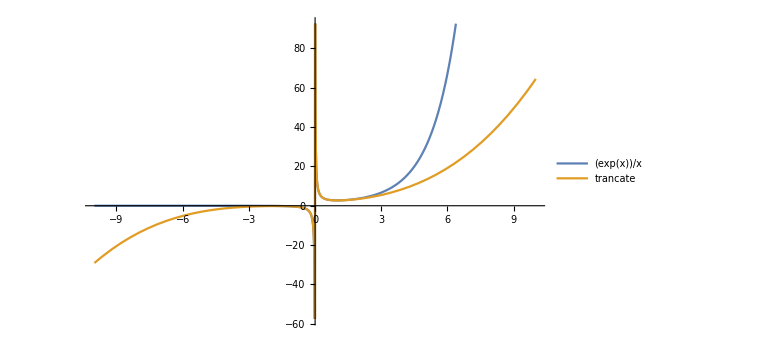

```mathematica
Plot[{Exp[x]/x, trancate}, {x,-10,10},
PlotLegends->"Expressions",
ImageSize->Large
]
```

```mathematica
ans2 = Series[Exp[x]/x, {x,0,12}]
```

1/x+1+x/2+x^2/6+x^3/24+x^4/120+x^5/720+x^6/5040+x^7/40320+x^8/362880+x^9/3628800+x^10/39916800+x^11/479001600+x^12/6227020800+O[x]^13

```mathematica
trancate2 = Normal[ans2]
```

1+1/x+x/2+x^2/6+x^3/24+x^4/120+x^5/720+x^6/5040+x^7/40320+x^8/362880+x^9/3628800+x^10/39916800+x^11/479001600+x^12/6227020800

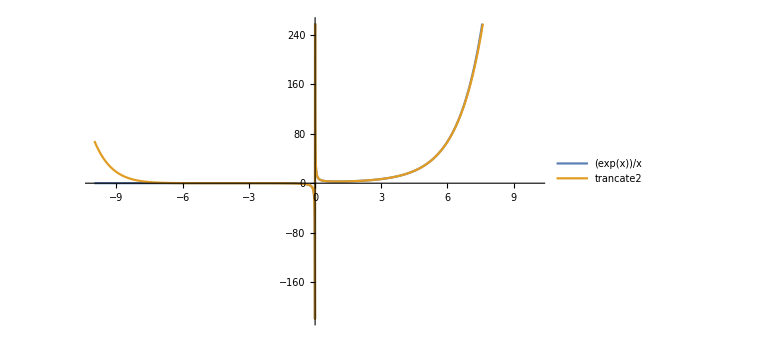

```mathematica
Plot[{Exp[x]/x, trancate2}, {x,-10,10},
PlotLegends->"Expressions",
ImageSize->Large
]
```

## Differential Equations

First Order ODE

```mathematica
Clear["Global`*"]
```

```mathematica
diffeq=D[x[t], {t,2}]==-w*w*x[t]
```

x''[t]==-w^2 x[t]

```mathematica
DSolve[diffeq,{x[t]},{t}]
```

{{x[t]→C[1] Cos[t w]+C[2] Sin[t w]}}

Second Order ODE

```mathematica
deqn=Cos[x]*D[y[x],{x,3}]-D[y[x],{x,2}]+Pi*D[y[x],x]==y[x]-x
```

π y'[x]-y''[x]+Cos[x] y^(3)[x]==-x+y[x]

```mathematica
DSolve[deqn,{y[x],y[x],y[x]},{x}]
```

DSolve[π y'[x]-y''[x]+Cos[x] y^(3)[x]==-x+y[x],{y[x],y[x],y[x]},{x}]